```mathematica
Modulo[{x_,y_}]:=Sqrt[x^2+y^2];
```

```mathematica
(*d es la abertura angular en cm. esc es el factor de escala. rcm distancia tierra cm (UA)*)
```

```mathematica
rcm=11;
```

```mathematica
esc=3;
```

```mathematica
xycm[d_]:=Tan[d*(1/esc)*(1/3600)*(Pi/180)]*rcm*(10^5);
```

```mathematica
(*componentes x e y de las posiciones angulares*)
```

```mathematica
datad1cm={{-4.4,2.8},{-5.2,-1.0},{-1.45,-6.75},{1.0,-7.5},{7.8,-3.5},{-3.7,3.5},{-1.0,-6.7},{6.8,3.1},{5.6,3.9},{2.4,5.8},{-4.4,2.8},{-5.5,0.9}};
```

```mathematica
datad2cm={{1.7,-1.2},{2.5,0.45},{1.1,3.4},{-0.6,3.9},{-3.85,1.8},{1.7,-1.7},{0.4,3.8},{-3.6,-1.5},{-3.1,-2.1},{-1.3,-3},{2.15,-1.4},{2.25,-0.2}};
```

```mathematica
(*componentes x e y en distancia en 10⁻⁵ pc*)
```

```mathematica
datar1cm=xycm[datad1cm];
```

```mathematica
datar2cm=xycm[datad2cm];
```

```mathematica
(*Generar el dibujo de los puntos*)
```

```mathematica
f1=ListPlot[datar1cm,Frame->True,FrameLabel->{Style["x𝒸ₘ / 10⁻⁵ pc",Bold,16],Style["y𝒸ₘ / 10⁻⁵ pc",16,Bold]},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Red,Yellow,Black}],Thick},PlotMarkers -> {{"x",15}},Epilog->{Black,PointSize@Large,Point[{0,0}]},PlotLegends->{"Observaciones m1"},PlotRange->{{-10,15},{-15,11}}];
```

```mathematica
f2=ListPlot[datar2cm,PlotMarkers -> {{"*",19}},PlotStyle->{Blend[{Blue, White}]},PlotLegends->{"Observaciones m2"}];
```

```mathematica
(*Fit a elipses*)
```

```mathematica
g1=ResourceFunction["EllipseFit"][datar1cm,{x,y}]
```

93.9772+3.40201 x-0.687235 x^2-1.95304 y-0.0797177 x y-0.722048 y^2==0

```mathematica
(*A1,B1,C1,D1,E1,F1*)
```

```mathematica
{A1,B1,C1,D1,E1,F1}={-0.6872352716890875,-0.07971772430284296,-0.7220476201597802,3.4020093186182643,1.953037084278905,93.97715060564829};
```

```mathematica
g2=ResourceFunction["EllipseFit"][datar2cm,{x,y}]
```

-23.2737+2.24049 x+0.745741 x^2-1.20118 y-0.0454413 x y+0.664684 y^2==0

```mathematica
(*A2,B2,C2,D2,E2,F2*)
```

```mathematica
{A2,B2,C2,D2,E2,F2}={0.7457412523130569,-0.04544129422509131,0.6646841907084163,2.240485498452707,1.201175768269202,-23.27366707894891};
```

```mathematica
(*gráficas elipses*)
```

```mathematica
graphg1=ContourPlot[g1,{x,-20,20},{y,-20,20},ContourStyle->Black,PlotLegends->{"Órbita de m1 respecto del CM"}];
```

```mathematica
graphg2=ContourPlot[g2,{x,-20,20},{y,-20,20},ContourStyle->Blue,PlotLegends->{"Órbita de m2 respecto del CM"}];
```

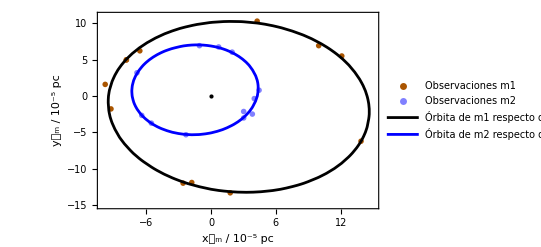

```mathematica
Show[f1,f2,graphg1,graphg2]
```

```mathematica
(*B1'=0 -> Angulo tal que este recto el eje de la elipse*)
```

```mathematica
FindRoot[(-0.7220476201597802+0.6872352716890875)*Sin[2*x]+(-0.07971772430284296)*(1-2*(Sin[x])^2)==0,{x,0}]
```

{x→-0.579531}

```mathematica
(*B2'=0 -> Angulo tal que este recto el eje de la elipse*)
```

```mathematica
FindRoot[0==(C2-A2)*Sin[2*x]+B2*(1-2*(Sin[x])^2),{x,0}]
```

{x→-0.255476}

```mathematica
(*funciones que nos pasan al sistema del eje rotado pero recto*)
```

```mathematica
f[θ_,{A_,B_,Ca_,Da_,Ea_,F_}]:={A*(Cos[θ])^2+B*Sin[θ]*Cos[θ]+Ca*(Sin[θ])^2,0,A*(Sin[θ])^2-B*Sin[θ]*Cos[θ]+Ca*(Cos[θ])^2,Da*Cos[θ]+Ea*Sin[θ],-Da*Cos[θ]+Ea*Sin[θ],F}
```

```mathematica
(*primera elipse rotada:*)
```

```mathematica
f[-0.5795307897171099,{A1,B1,C1,D1,E1,F1}]
```

{-0.661148,0,-0.748135,1.77698,-3.91607,93.9772}

```mathematica
(*segunda elipse rotada:*)
```

```mathematica
f[-0.25547579374506163,{A2,B2,C2,D2,E2,F2}]
```

{0.751675,0,0.65875,1.86422,-2.47131,-23.2737}

```mathematica
(*ecuaciones de las elipses rotadas*)
```

```mathematica
g1x=-0.6611477246129933*x^2-0.7481351672358744*y^2+1.7769837719257429*x-3.916072635808821*y+93.97715060564829==0;
```

```mathematica
g2x=0.7516754981626701*x^2+0.6587499448588032*y^2+1.8642223708156673*x-2.4713105094112344*y-23.27366707894891==0;
```

```mathematica
(*SEMIEJES MAJORES DE AMBAS ORBITAS*)
```

```mathematica
a1=Sqrt[((1.7769837719257429/(2*Sqrt[-0.6611477246129933]))^2+(-3.916072635808821/(2*Sqrt[-0.7481351672358744]))^2-(93.97715060564829))/(-0.6611477246129933)]
```

12.3166+0. ⅈ

```mathematica
a2=Sqrt[((1.8642223708156673/(2*Sqrt[0.7516754981626701]))^2+(-2.4713105094112344/(2*Sqrt[0.6587499448588032]))^2-(-23.27366707894891))/(0.7516754981626701)]
```

5.9652

```mathematica
(*----------------------------------------------------------------*)
```

```mathematica
(*----------------------------------------------------------------*)
```

```mathematica
(*----------------------------------------------------------------*)
```

```mathematica
(*M1/M2*)
```

```mathematica
(*Normas de datar1cm*)
```

```mathematica
normr1cm={Norm[{-7.821660722032338,4.977420459425207}],Norm[{-9.243780853372746,-1.7776501640698463}],Norm[{-2.577592737903751,-11.999138607936947}],Norm[{1.7776501640698463,-13.332376231165094}],Norm[{13.865671280467103,-6.221775574305396}],Norm[{-6.577305607131093,6.221775574305396}],Norm[{-1.7776501640698463,-11.910256099723034}],Norm[{12.088021116151015,5.510715508657827}],Norm[{9.95484091905424,6.932835639958162}],Norm[{4.266360393785309,10.310370951898069}],Norm[{-7.821660722032338,4.977420459425207}],Norm[{-9.77707590263311,1.599885147662597}]};
```

```mathematica
(*Normas de datar2cm*)
```

```mathematica
normr2cm={Norm[{3.022005278923711,-2.133180196884632}],Norm[{4.444125410194927,0.7999425738308754}],Norm[{1.9554151804771887,6.0440105578930385}],Norm[{-1.066590098441313,6.932835639958162}],Norm[{-6.843953131751261,3.199770295331963}],Norm[{3.022005278923711,-3.022005278923711}],Norm[{0.7110600656274186,6.755070623544449}],Norm[{-6.399540590718076,-2.6664752461076713}],Norm[{-5.510715508657827,-3.7330653445577595}],Norm[{-2.3109452132921886,-1100000 Tan[π/648000]}],Norm[{3.821947852762222,-2.4887102296998647}],Norm[{3.999712869171299,-0.3555300328136722}]};
```

```mathematica
m1m2=normr2cm/normr1cm
```

{0.398988,0.479706,0.517602,0.521503,0.497119,0.47204,0.56405,0.521859,0.548682,0.520884,0.491939,0.405313}

```mathematica
(*MEDIA M1/M2*)
```

```mathematica
mediam1m2=Total[m12]/12
```

0.494974

```mathematica
(*SEMIEJE RELATIVO*)
```

```mathematica
a=a1+a2;
```

```mathematica
(*----------------------------------------------------------------*)
```

```mathematica
aenmetros=a*10^(-5)*3.0857*10^(16)
```

5.64123×10^12+0. ⅈ

```mathematica
Paños=79.419;
```

```mathematica
Psegundos=79.419*(365)*24*3600
```

2.50456×10^9

```mathematica
G=6.6743*10^(-11);
```

```mathematica
m2=(4*Pi^2*(aenmetros)^3)/(1.5*G*(Psegundos)^2)
```

1.12855×10^31+0. ⅈ